# Decomposition of linear optics network into H*D*H^dag where H is 4x4 Hadamard and D is phases

## Hadamard operations

### 2 mode

```mathematica
H=1/(√2){{1,1},{1,-1}};
H // MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

### 4 mode

```mathematica
H2=KroneckerProduct[H,H];
H2 // MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

### Phase matrix

```mathematica
phases=DiagonalMatrix[{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3],Subscript[ϕ, 4]}];
phases // MatrixForm
```

(ϕ_1 | 0 | 0 | 0
0 | ϕ_2 | 0 | 0
0 | 0 | ϕ_3 | 0
0 | 0 | 0 | ϕ_4)

## How mixing is matrix M? (1 = perfect mixing)

```mathematica
mixing[M_]:=1/4^3(∑_(i=1)^4 ∑_(j=1)^4 Abs[M⟦i,j⟧])^2
```

## Four mode Hadamard is perfectly mixing

```mathematica
mixing[H2]
```

1

## General form for H.phases.H^dag and its mixing

```mathematica
U=H2.phases.Transpose[H2];
U // MatrixForm
Print["mixing = ",FullSimplify[mixing[U]]]
```

(ϕ_1/4+ϕ_2/4+ϕ_3/4+ϕ_4/4 | ϕ_1/4-ϕ_2/4+ϕ_3/4-ϕ_4/4 | ϕ_1/4+ϕ_2/4-ϕ_3/4-ϕ_4/4 | ϕ_1/4-ϕ_2/4-ϕ_3/4+ϕ_4/4
ϕ_1/4-ϕ_2/4+ϕ_3/4-ϕ_4/4 | ϕ_1/4+ϕ_2/4+ϕ_3/4+ϕ_4/4 | ϕ_1/4-ϕ_2/4-ϕ_3/4+ϕ_4/4 | ϕ_1/4+ϕ_2/4-ϕ_3/4-ϕ_4/4
ϕ_1/4+ϕ_2/4-ϕ_3/4-ϕ_4/4 | ϕ_1/4-ϕ_2/4-ϕ_3/4+ϕ_4/4 | ϕ_1/4+ϕ_2/4+ϕ_3/4+ϕ_4/4 | ϕ_1/4-ϕ_2/4+ϕ_3/4-ϕ_4/4
ϕ_1/4-ϕ_2/4-ϕ_3/4+ϕ_4/4 | ϕ_1/4+ϕ_2/4-ϕ_3/4-ϕ_4/4 | ϕ_1/4-ϕ_2/4+ϕ_3/4-ϕ_4/4 | ϕ_1/4+ϕ_2/4+ϕ_3/4+ϕ_4/4)

mixing = 1/64 (Abs[ϕ_1+ϕ_2-ϕ_3-ϕ_4]+Abs[ϕ_1-ϕ_2+ϕ_3-ϕ_4]+Abs[ϕ_1-ϕ_2-ϕ_3+ϕ_4]+Abs[ϕ_1+ϕ_2+ϕ_3+ϕ_4])^2

## We get the identity when there are no phases

```mathematica
Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm
mixing[Udash]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

1/4

## Some examples with non - zero phases

```mathematica
(* With a single π/2 phase on one mode *)
Udash=U /. {Subscript[ϕ, 1]->ⅇ^(ⅈ π/2),Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^(ⅈ π/2),Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^(ⅈ π/2),Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^(ⅈ π/2)};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

(* With two π/2 phases on two modes *)
Udash=U /. {Subscript[ϕ, 1]->ⅇ^(ⅈ π/2),Subscript[ϕ, 2]->ⅇ^(ⅈ π/2),Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^(ⅈ π/2),Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^(ⅈ π/2),Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^(ⅈ π/2),Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^(ⅈ π/2)};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^(ⅈ π/2),Subscript[ϕ, 3]->ⅇ^(ⅈ π/2),Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^(ⅈ π/2),Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^(ⅈ π/2)};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]

Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^(ⅈ π/2),Subscript[ϕ, 4]->ⅇ^(ⅈ π/2)};
Udash // MatrixForm // N
Print["mixing=",mixing[Udash] // N]
```

(0.75+0.25 ⅈ | -0.25+0.25 ⅈ | -0.25+0.25 ⅈ | -0.25+0.25 ⅈ
-0.25+0.25 ⅈ | 0.75+0.25 ⅈ | -0.25+0.25 ⅈ | -0.25+0.25 ⅈ
-0.25+0.25 ⅈ | -0.25+0.25 ⅈ | 0.75+0.25 ⅈ | -0.25+0.25 ⅈ
-0.25+0.25 ⅈ | -0.25+0.25 ⅈ | -0.25+0.25 ⅈ | 0.75+0.25 ⅈ)

mixing=0.856763

(0.75+0.25 ⅈ | 0.25-0.25 ⅈ | -0.25+0.25 ⅈ | 0.25-0.25 ⅈ
0.25-0.25 ⅈ | 0.75+0.25 ⅈ | 0.25-0.25 ⅈ | -0.25+0.25 ⅈ
-0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.75+0.25 ⅈ | 0.25-0.25 ⅈ
0.25-0.25 ⅈ | -0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.75+0.25 ⅈ)

mixing=0.856763

(0.75+0.25 ⅈ | -0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.25-0.25 ⅈ
-0.25+0.25 ⅈ | 0.75+0.25 ⅈ | 0.25-0.25 ⅈ | 0.25-0.25 ⅈ
0.25-0.25 ⅈ | 0.25-0.25 ⅈ | 0.75+0.25 ⅈ | -0.25+0.25 ⅈ
0.25-0.25 ⅈ | 0.25-0.25 ⅈ | -0.25+0.25 ⅈ | 0.75+0.25 ⅈ)

mixing=0.856763

(0.75+0.25 ⅈ | 0.25-0.25 ⅈ | 0.25-0.25 ⅈ | -0.25+0.25 ⅈ
0.25-0.25 ⅈ | 0.75+0.25 ⅈ | -0.25+0.25 ⅈ | 0.25-0.25 ⅈ
0.25-0.25 ⅈ | -0.25+0.25 ⅈ | 0.75+0.25 ⅈ | 0.25-0.25 ⅈ
-0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.25-0.25 ⅈ | 0.75+0.25 ⅈ)

mixing=0.856763

(0.5+0.5 ⅈ | 0. | -0.5+0.5 ⅈ | 0.
0. | 0.5+0.5 ⅈ | 0. | -0.5+0.5 ⅈ
-0.5+0.5 ⅈ | 0. | 0.5+0.5 ⅈ | 0.
0. | -0.5+0.5 ⅈ | 0. | 0.5+0.5 ⅈ)

mixing=0.5

(0.5+0.5 ⅈ | -0.5+0.5 ⅈ | 0. | 0.
-0.5+0.5 ⅈ | 0.5+0.5 ⅈ | 0. | 0.
0. | 0. | 0.5+0.5 ⅈ | -0.5+0.5 ⅈ
0. | 0. | -0.5+0.5 ⅈ | 0.5+0.5 ⅈ)

mixing=0.5

(0.5+0.5 ⅈ | 0. | 0. | -0.5+0.5 ⅈ
0. | 0.5+0.5 ⅈ | -0.5+0.5 ⅈ | 0.
0. | -0.5+0.5 ⅈ | 0.5+0.5 ⅈ | 0.
-0.5+0.5 ⅈ | 0. | 0. | 0.5+0.5 ⅈ)

mixing=0.5

(0.5+0.5 ⅈ | 0. | 0. | 0.5-0.5 ⅈ
0. | 0.5+0.5 ⅈ | 0.5-0.5 ⅈ | 0.
0. | 0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0.
0.5-0.5 ⅈ | 0. | 0. | 0.5+0.5 ⅈ)

mixing=0.5

(0.5+0.5 ⅈ | 0.5-0.5 ⅈ | 0. | 0.
0.5-0.5 ⅈ | 0.5+0.5 ⅈ | 0. | 0.
0. | 0. | 0.5+0.5 ⅈ | 0.5-0.5 ⅈ
0. | 0. | 0.5-0.5 ⅈ | 0.5+0.5 ⅈ)

mixing=0.5

(0.5+0.5 ⅈ | 0. | 0.5-0.5 ⅈ | 0.
0. | 0.5+0.5 ⅈ | 0. | 0.5-0.5 ⅈ
0.5-0.5 ⅈ | 0. | 0.5+0.5 ⅈ | 0.
0. | 0.5-0.5 ⅈ | 0. | 0.5+0.5 ⅈ)

mixing=0.5

## Search through phases to find maximally mixing decomposition

```mathematica
delta=2π/2;
sols={};

mMax=0;
For[phi1=0,phi1≤2π,phi1+=delta,
For[phi2=0,phi2≤2π,phi2+=delta,
For[phi3=0,phi3≤2π,phi3+=delta,
For[phi4=0,phi4≤2π,phi4+=delta,
thisU=U /. {Subscript[ϕ, 1]->N[ⅇ^(ⅈ phi1)],Subscript[ϕ, 2]->N[ⅇ^(ⅈ phi2)],Subscript[ϕ, 3]->N[ⅇ^(ⅈ phi3)],Subscript[ϕ, 4]->N[ⅇ^(ⅈ phi4)]};
m=mixing[thisU];
If[m>mMax,
mMax=m;
sols={Subscript[ϕ, 1]->ⅇ^(ⅈ phi1),Subscript[ϕ, 2]->ⅇ^(ⅈ phi2),Subscript[ϕ, 3]->ⅇ^(ⅈ phi3),Subscript[ϕ, 4]->ⅇ^(ⅈ phi4)};
];
];
];
];
];

Print["Maximum mixing = ",mMax];
Print["Phases = ",sols];
Usol=U /.sols;
Usol // MatrixForm
```

Maximum mixing = 1.

Phases = {ϕ_1→1,ϕ_2→1,ϕ_3→1,ϕ_4→-1}

(1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
-1/2 | 1/2 | 1/2 | 1/2)

## Minimally mixing decomposition (identity matrix when phases are zero)

```mathematica
Udash=U /. {Subscript[ϕ, 1]->ⅇ^0,Subscript[ϕ, 2]->ⅇ^0,Subscript[ϕ, 3]->ⅇ^0,Subscript[ϕ, 4]->ⅇ^0};
Udash // MatrixForm
Print["mixing = ",mixing[Udash]];
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

mixing = 1/4

## Set ϕ_1,ϕ_2,ϕ_3=0 and vary ϕ_4 to tune between maximally and minimally mixing

1/64 (3 Abs[1-ⅇ^(ⅈ newPhi4)]+Abs[3+ⅇ^(ⅈ newPhi4)])^2

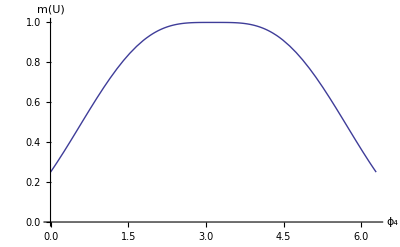

```mathematica
mix=FullSimplify[mixing[U /. {Subscript[ϕ, 1]->1,Subscript[ϕ, 2]->1,Subscript[ϕ, 3]->1,Subscript[ϕ, 4]->ⅇ^(newPhi4 ⅈ)}]]
Plot[mix,{newPhi4,0,2π},PlotStyle->Thick,PlotRange->{0,1},AxesLabel->{"ϕ_4","m(U)"},BaseStyle->{FontSize->14}]
```